Math254 - Written Homework 1

```mathematica
f[x_,y_]:=-(x^2-1)^2-(x^2y-x-1)^2
fxx=D[f[x,y],x,x]
fyy=D[f[x,y],y,y]
fxx*fyy/.{x->1,y->2}
bounds:=2
surface:= Plot3D[f[x,y], {x,-1,1}, {y,0,2}, ImageSize->Large, AxesLabel->Automatic]
critPointRules:=Solve[Grad[f[x,y],{x,y}]=={0,0} && -bounds≤ x ≤ bounds && -bounds ≤ y ≤ bounds]
```

-8 x^2-4 (-1+x^2)-2 (-1+2 x y)^2-4 y (-1-x+x^2 y)

-2 x^4

52

```mathematica
critPoints={x,y,f[x,y]}/.critPointRules
```

{{-1,0,0},{1,2,0}}

```mathematica
pts:=ListPointPlot3D[critPoints, PlotStyle->{PointSize[0.03],Black}]
```

```mathematica
Show[surface,pts]
```

-Graphics3D-

{{-1,0},{1,2}}

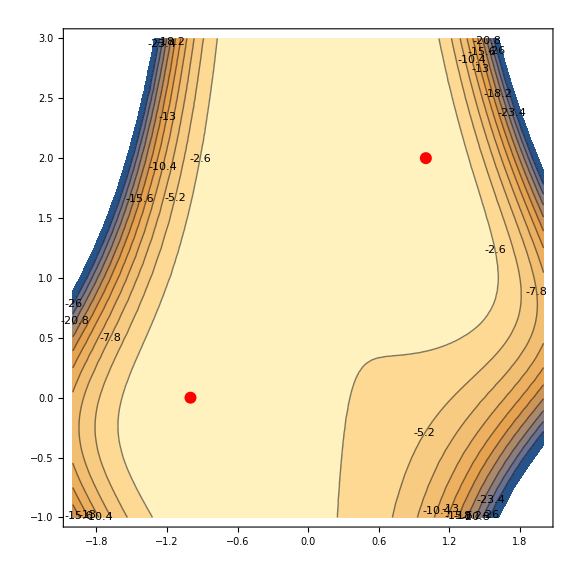

```mathematica
xyPts={x,y}/.critPointRules (*Make the critical point rules into points in the (x,y) plane *)
Show[
ContourPlot[f[x,y],{x,-2,2},{y,-1,3},Contours->10,ContourLabels->True],
ListPlot[xyPts,PlotStyle->{Red,PointSize[0.015]}],
ImageSize->Large
]
```